Да се намери полином от втора степен на най-добро средноквадратично приблицение в интервала [0, Pi/2] при тегло u(x) = 1 за функцията f(x) = sinx. Да се илюстрира графично. Да се намерят равномерното и средноквадратичното разстояние между полинома и функцията.

TODO: дефинирай смисъла на теглото

```mathematica
u[x_]:=1
SrednoKvadrat[diff_,x_,a_,b_]:=√(∫_a^b u[x]*(diff[x])^2 ⅆx)
```

```mathematica
f[x_]=a*x^2+b*x+c
```

c+b x+a x^2

```mathematica
diff[x]=Sin[x]-f[x]
```

-c-b x-a x^2+Sin[x]

```mathematica
uravnenie[a_,b_,c_]=SrednoKvadrat[diff,x,0,Pi/2]
```

√(4 a-2 c+1/4 (1+2 c^2) π+1/4 b c π^2+1/24 (b^2+2 a c) π^3+1/32 a b π^4+(a^2 π^5)/160-2 (b+a π))

```mathematica
sol=NSolve[{D[uravnenie[a,b,c],a]==0,D[uravnenie[a,b,c],b]==0,D[uravnenie[a,b,c],c]==0},{a,b,c}]
```

{{a→-0.33824,b→1.19575,c→-0.0243249}}

```mathematica
poly[x_]=f[x]/.sol[[1]]
```

-0.0243249+1.19575 x-0.33824 x^2

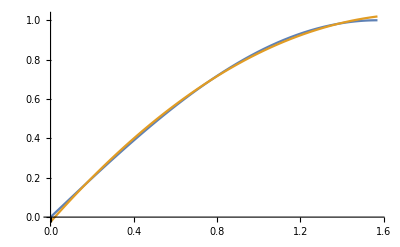

```mathematica
Plot[{Sin[x],poly[x]},{x,0,Pi/2}]
```

```mathematica
ravnomernoRazst=MaxValue[{poly[x]-Sin[x],0≤x≤Pi/2},x]
```

0.0193732

```mathematica
srednoRazst=√(∫_0^(Pi/2) (poly[x]-Sin[x])^2 ⅆx)
```

0.0105051